# EMRIs with environment

## Waveform from hybrid approach in vacuum

Here, we use the hybrid approach SF+PN introduced by Honet, Pound and Compère, 2025. to compute waveforms for the inspiral phase in vacuum. The goal is to reproduce their main results/ plots.

In the following, we use the BHPT Teukolsky package:

```mathematica
<<KerrGeodesics`
<<Teukolsky`
```

## Computation of the energy fluxes

To construct the hybrid energy fluxes, we need to compute the energy fluxes at 1 SF (by interpolating from BHPT toolkit data), at 4PN and evaluate the common terms. One can then trace the hybrid energy flux. Finally, we will compare it to NR data to reproduce the Fig. 9. of the reference paper.

### Energy fluxes in Self-force

#### Evaluate the fluxes at the nodes

To compute the energy fluxes at 0PA, one first has to get the data on which we can then interpolate. We use the BHPT Teukolsky package:

First, we construct the 2D grid of Chebyshev nodes:

```mathematica
nR = 18;
nχ = 27;

nodesX = Table[Cos[(2 i +1)π /(2 nR )], {i, 0, nR-1}];
nodesY = Table[Cos[(2 j +1)π /(2 nχ )], {j, 0, nχ-1}];
lmax = 5;
Ndigit = 64;
```

Then, we construct the function giving the energy flux for a point in the grid:

```mathematica
fluxesAtPhasePoint[rc_, χc_]:= With[{rp= 2 KerrGeoISCO[χc, 1]/(1+rc),e=0,xInc=1, s=-2,n=0,k=0},
With[{orbit=KerrGeoOrbit[N[χc, Ndigit],N[rp, Ndigit],e,xInc]},
2 Total[ Flatten[ Table[With[{flux = TeukolskyPointParticleMode[s, l, m, n, k, orbit]["EnergyFlux"]},
{flux["ℐ"], flux["ℋ"]}
],
{l, 2, lmax}, {m, 1, l}],
1]
]
]
];
```

Here, circular equatorial orbit: we can avoid summing on negative m and multiply by 2 instead, and the flux vanishes at m=0.

Finally, we evaluate the function on the 2D grid:

```mathematica
fluxesGrid = Outer[fluxesAtPhasePoint, nodesX, nodesY]
```

{{{0.0764350529379169355996760246114744,-0.0106426814302379141797572992},{0.080025175819120354414424111266511686,-0.007297385624057132392797297177788334},{0.059360464716022812740841747594559225,-0.003646239561411704970214236016641315},{0.040120550457454074016772814463819998,-0.0016501881155960941151716456977173734},{0.0262008871224371453426182311857649,-0.00070990709118660452270613959717393157},{0.016965424188224488600039881718677,-0.00029581617256778812292643832565980784},{0.01104455527151895216267153245449166142046,-0.0001198413457659005070828427176880197327114358},{0.0072861875982190646366434338870192338302505584,-0.00004657772784895779765422721605445277724615297864},{0.00489313130611432468235982933805809747491252459,-0.0000165104722520453207683988301750358532838415284064},{0.003353603210803297092133590277305911711412212931,-4.3522208924532802528165536418369371468746204720656×10^-6},{0.00234889845935050317243410791164268969923843368189,4.51987418550147491962969772652149213598725238513086×10^-7},{0.00168238156315724629440012685515559261835545168517,2.263106390039480934475416337638363695242167943537307×10^-6},{0.001232496845078866525179045373711702942872760954407,2.8698611231220293430454786386194479302291005533846593×10^-6},{0.00092348542145446644500440833359444349273130644154869,3.0008069457584229937996592425045116549961881726623785×10^-6},{0.000707577552148443464094987672412731259085124381807,2.95030150983700642558067553856981076284332465058207×10^-6},{0.000554241385429097982992581857983595351548587614863,2.83616836942816313394345466192837676120785631044817×10^-6},{0.0004436788897794874204503163234530142381757483741,2.705131672584665629639919777177734259825443957227×10^-6},{0.0003628626964908087503422079695314527239350486258212,2.5756154358594125943237301515011323709003881676525×10^-6},{0.0003030965570204661469126609859267196908161936379437,2.4549195334292350061748526907653502855227553814069×10^-6},{0.0002584959290334817162337116591059953216863986724452,2.3460056873961716032281263012470099261424041430981×10^-6},{0.0002250298236029561711220376226233460440253369900928,2.2501268684783087277564202029092091118071396344975×10^-6},{0.0001999090938405901582676428260659521361804621179391,2.1678269466326299548966013343850858084090049098361×10^-6},{0.0001811914235052720141412499245135667555207850483181,2.09932069411420444106911827811212074892282182085363×10^-6},{0.0001675238866813920781546475913279437314750172024888,2.04464985557260862607977217155274673583932264168044×10^-6},{0.0001579743687851810856679843160981199710350412278064,2.0037641982027154927168694805087107816496992979074×10^-6},{0.0001519216664112401764646081033052739347796535620588,1.9765771612211617386972817306082076193252307213338×10^-6},{0.00014898557232245043217750805783306330618257952027,1.963007506104680646873810421366609136663542299613×10^-6}},{{0.0781246489393556774865451769537463,-0.0107701622428351700480576335},{0.077843477083992351033048921682786035,-0.007022356665890604410111572689874591},{0.056705952182734321952190264618927223,-0.003441207284080456648498672122983039},{0.037904023584652601416518485759063453,-0.0015383962010961615439062881068649525},{0.0245640070400861714698748709857091,-0.00065626757850466426464160668812569804},{0.01581740115771851551850943713952989082,-0.000271955731425322912940661631856548307214},{0.0102548597429123116295629999194871086559802,-0.00010988346616852480709344754932884832374930909},{0.0067441641981100974479640404523891767391051595,-0.000042777776358097325270988125984492965634086925183},{0.00451825816191829766806020749863689785667819843,-0.0000153391324922141183413289888926574411041277132475},{0.0030908484183638713446077959814651409359988750169,-4.2619341776719381568183007678895494481454641197637×10^-6},{0.00216162028633034214420037111763049313197566103853,1.22552151899969808918980168048991184306689001426819×10^-7},{0.001546376760308728866989043116749697834258827614564,1.790158087763409100793485640544182924882012284006533×10^-6},{0.001131747914671307792695630720204352794580100837991,2.365415724844774470073340875611305302041986176711657×10^-6},{0.00084731184557472394126926600704026224873511723564893,2.5080004460662021603056420933628748511525158717975661×10^-6},{0.000648779717304147414245083472908663392258061293611,2.48389075360772003210099884581628518656316629160459×10^-6},{0.00050790331477380550884493605416175213392088433142,2.39950999363793629896548066112759058247753565318203×10^-6},{0.0004063962575925716478656474011920088585875005436695,2.29719244751426121586566622004532216823990794297763×10^-6},{0.0003322424992016996146689052109310081824807965367565,2.1938085631427305710586031182628113561307936062789×10^-6},{0.0002774300787362322610796128311067439714251014232129,2.09621794938307676145609415761373916813816954273076×10^-6},{0.0002365426826411107430003369181269554291953607492092,2.0073574367323510124179110935340599670842898372236×10^-6},{0.0002058730411059240813929499049911741981653355078325,1.9285951244144594901196126525161290952365447197622×10^-6},{0.0001828577222810486500245557497082644859514678767541,1.86062536444941089657433888481870801290096247825982×10^-6},{0.0001657125958123802286141823186583595398425453850072,1.80381079591698384696700856660099941158790418987306×10^-6},{0.00015319549503095037712654174395930141392390224061356,1.75832492198198078668552505326410609499870974846844×10^-6},{0.000144450932356029602217196360746950774616507377992,1.724227637519755947355853158126856791673440226741×10^-6},{0.000138908935271484321217898416858360448659414267827,1.7015176445615048383670460168567572541394989916903×10^-6},{0.00013622072335286117837920956424358819214196655112,1.690171801040130121047307044621363417344009909686×10^-6}},{{0.0804776690610319705246168607045016865,-0.010814612436891517728736201828928725},{0.0733849288969766922791635972723499346,-0.006455223618504563138859573951185012},{0.0516378760608917837234293466880518497,-0.00304918182474320617482149685590842531},{0.033782390945508535594428512124679139,-0.0013313222847474850552635567705772341},{0.0215685847833644061450767379103242,-0.00055870020266607897980550714727216152},{0.013739382498787501756292803127890028767,-0.0002289747115938541471672495062092152825434},{0.00883654317560389345216084241712903236525617,-0.0000919667148076058026747654352459613899756561585},{0.00577623277393644928432616102484704601764066112,-0.000035849113487819145442219093462917156543312630228},{0.00385169530677895060406936734097522632746592215,-0.00001307744548333006238991037568239083913452910313987},{0.0026251837036192929406676144917880951895033902267,-3.922489296759235097038444536976881869458642616519×10^-6},{0.00183057237493816643144658300985851877438975893017,-2.943293029324566013701163655412114723870478231927582×10^-7},{0.001306453724205455457971362179620676927775313712346,1.10297953603319650076734122279045969236912710326039×10^-6},{0.00095430935720663820771235466324087256889888173913498,1.6059268218425886891939269958806235540569602405409564×10^-6},{0.00071333279665642572987461712254474179633700071682239,1.75378126154861762592990440050072883531970255053912834×10^-6},{0.000545473971177442115861150091282070532813688529869,1.7629002864261526192498421827725438663800111895103×10^-6},{0.0004265611970484983502632910987829224548699755912039,1.71963207693072947243234583995197480009505877449987×10^-6},{0.0003409980421558823753256677627040476874433059322997,1.6584122466244413890306590949344288696110581012741×10^-6},{0.0002785635370650156398581214772585339681214135297038,1.59315146058951919360350491776693738749284378804519×10^-6},{0.0002324578246991763857377026388936628754993368071532,1.52971056994120753922269138921450380976669329712893×10^-6},{0.0001980925849123969142906194078035542457482269303642,1.47078315670793338077988346836229598929937212489913×10^-6},{0.0001723322007712780728780925943377872113366244249629,1.41777168009197677805261546945695719245281052326816×10^-6},{0.00015301136969409449774493734462788904642794126898103,1.37149774925349455993273543089286504229103278403747×10^-6},{0.00013862471371567039667106475959361979016693138548054,1.33247419422853195148532878311549439091762408358647×10^-6},{0.00012812509291302410976471932715334285873102841482541,1.30102030055293560345847178678863701424919941815602×10^-6},{0.00012079186243282008360918540748447943631026842169475,1.2773244782817201416344534003269906470660521775266×10^-6},{0.0001161451596004751749859166251859767250771504817766,1.2614885507109422920735723319828922255461502682725×10^-6},{0.00011389146202867660743740943571170915417116733938,1.253561290492389478986835390245267686271269985378×10^-6}},{{0.0816599334369481996239348746699876127,-0.01046416985554494428596424831074658},{0.0665315689463192770153140240839335411,-0.0055925981438119278224978153649318017},{0.0446092571213628213824613077093587112,-0.00251146544807495292394483947095709711},{0.02830676078752328827269529362033283,-0.0010607041995403756210570389423774016},{0.0176924867483687733092260633815626,-0.00043485054127965643341743636564937267},{0.011098181227756831825447027412945805127105,-0.000175332878123715181712950613189717473795233},{0.0070567340463060732967656856036262398427673324,-0.00006972477718925440933313038917834222956954601109},{0.00457295970133837993509438112054126854210825373,-0.000027137713963644052271621886966083062956461155211},{0.0030289081591776144858075474815267197298805567812,-0.00001005591641323073900661941813696977775262581662116},{0.0020534985361013216316559938289197185983490714183,-3.24077352614994280624117532562977666719410666090338×10^-6},{0.001425879374246592061207525084661272130227917150266,-5.44878193707957967200245620413288312475788193209745×10^-7},{0.001014147059994508173017304241686035875451840159,5.0357486036672247278366781447228856299377147470204091×10^-7},{0.00073871641103716423305423905204282732930193469032361,8.95774235266003350553372260113454496279127125133135521×10^-7},{0.000550903265610517881142113178738833974681260735232203,1.02775312308737960722001953711911998867981569167427389×10^-6},{0.000420457311935223377514611986206800090249235182333,1.05703292627493069542217852394477197723521147628716×10^-6},{0.0003282704920366537219916736977918285804792129928696,1.04605310735447367745633837305748889581456217281879×10^-6},{0.0002620706002200133861009168096130669162498916972972,1.01965087656338468397382200911723865367607986003714×10^-6},{0.0002138458924481509836280496925898340219738376122001,9.87935786081817325764929381280417485218350694553794×10^-7},{0.0001782832597113555207911842687423214624077692873791,9.55288700809943436924728154986214853898534095712735×10^-7},{0.00015180718019533505282235619008326893962900390419288,9.23844339576517491647347041026774545342160179157163×10^-7},{0.00013197968009797959325332858545057939349122192672563,8.94812434186298306087723753717782415223361946906817×10^-7},{0.00011712040938434276751470370324823306920255496241727,8.68970980713519218333308608821465677389979871386782×10^-7},{0.0001060629989028739568051607108707436109221602533986,8.46853009292292016904956768183144823008178220710706×10^-7},{0.000097997188755107315225601108567054167410170293099131,8.28825717069546068435423281357836967931732029628441×10^-7},{0.000092365946360521494049927178678031550322596760307848,8.1513432954127998677952577807541559078352880885066×10^-7},{0.00008879865842778650977353275285669258568056485554577,8.0593383623180347834685631494677706329213552536366×10^-7},{0.000087068760248581443247785223680232473548134738261,8.013134412741457209062039799419710734614013147918×10^-7}},{{0.079582292405970592460456488625026526,-0.00947128034024862565440769245252257},{0.057330155769420760279981439670838848,-0.0044857725937509199249251571138393491},{0.0362653777991104844340953345695721736,-0.0018957601412230830166040871068953265},{0.02216466889788921340182040419100526,-0.000768811257390278965988455202312892872},{0.01349533869694950895791030565265163554,-0.000306222428086008627419162994253340185088},{0.00830627525458394696165091073011804169221125,-0.00012093579858399001890894630752767253080993329},{0.00520745152864862888490093776298759796029697808,-0.000047426303372593565197329007523265371833643746242},{0.003338462420911690896441725968466939788066680553,-0.00001835227017976595084639247963710413241371336094277},{0.002192816922419585189541078941737460743772133165,-6.8656713042131654226411848647903675369887555744583×10^-6},{0.0014768492374588309012055484817660523138374769964,-2.33467989008015226008035973120617748011012739860188×10^-6},{0.001020037437075498999871131605442076910815263495158,-5.538246814041258074791595801108698157067180361169332×10^-7},{0.00072236595364038278498407787994025118682934527994712,1.4087055649031093746834150193099878257296122089868324×10^-7},{0.000524314886857700877948149659613272945040410340441478,4.07405341613188299933157912644619136771876282504830247×10^-7},{0.000389863547750741083618856450243264398367686945897626,5.05333858056810589986454008585684007509210067331151617×10^-7},{0.0002968208788645147575277092069261320563602050167789,5.36625467996859741907957581634938680337838129186038×10^-7},{0.0002312663950717611909815369377669419150850186207062,5.41218530658791520566743396905839907166542052468794×10^-7},{0.00018431037533731247638303513973033319484050352314563,5.34836999307701935571833859713434441385748536570432×10^-7},{0.00015017665631451883192200154450245202439248924286734,5.23854541396924966732849166067910340533336782079999×10^-7},{0.00012504982653721382427469101835414530807056315652885,5.11064567017154674812897807324485663468311296284804×10^-7},{0.00010637081225813192053308806374048464670712197381566,4.97878273388603801517378021767795096693653135812329×10^-7},{0.000092399621509807808812757415199019355404849161071443,4.85141871445032739794316937756861739712372958982126×10^-7},{0.000081939836191205919979514362898225535479899627023896,4.7343359317585505429074917818550883192336827573802×10^-7},{0.00007416265576170475560262822312332141261735259533402,4.63172394244056749738072024846738433123397593169267×10^-7},{0.000068493278457635504435196795177335676492609910487264,4.54662669857329767360466187986615657440986294140886×10^-7},{0.000064537072326212433346340017069424109479303161505026,4.481190926499296120466964117061012636576039144978×10^-7},{0.00006203174688323138654786045906930698539339095385026,4.4368513143540270209271504456601587187561395894607×10^-7},{0.000060817076181467786028280522386930598649345592268,4.414477468463761824553859399009803351729318878587×10^-7}},{{0.0727122039440562698873887963152155,-0.007800854216269884682551982270880506},{0.0462397156510162552556965787513227392,-0.00326111006659561824670860205827568356},{0.0274274266294373344204777482244615,-0.0012882121299398489380070628836482764},{0.0160731520222491680238849423891154,-0.00049918351597210994564454560901665899},{0.0095031284269583784154639008896539490995921,-0.0001924620698430701079594273453545260207610463},{0.0057258002131580965650608421134992454837264518,-0.00007421125370668843414145160624385375748623890284},{0.003533022477188819497893574277971510431629670507,-0.0000286044154349272772437125860787872225133000153759},{0.0022375907748256839652331828710345557550356188639,-0.0000109576065893746283113080757847654770603466966274},{0.00145581070583562746573058750794561598873319350122,-4.10809778914693782118053296512182926598929150574623×10^-6},{0.0009730887838328775046846397558910725750711754243913,-1.445084740911830627300975638672359510514657969931789×10^-6},{0.00066800520353166920693741511774148332492780687126321,-4.0975696439418053239626830756537926155450639594605384×10^-7},{0.00047071027142705261942440078699914093013953977931209,-7.68835349322915432308807181145774164510787659266011223×10^-9},{0.000340251471242679052153259470379136799921069429743003,1.481965717137333927256406486489668829102886672850169911×10^-7},{0.0002521346818243763900017214840391929236556123404063567,2.083300185991770117978490920839945841008208538578003861×10^-7},{0.0001914119466959092680245632510164427984489301286557,2.309261482243184422092811903331747223401678828291321×10^-7},{0.00014877848679341418936139028412221547645037789886788,2.384164846891574456329225621226352913189454684843729×10^-7},{0.00011833000727242714250717211755490186153598718798386,2.394758175666737976794724943416908017559745167228127×10^-7},{0.000096250548755353706920129568750290297432112704992462,2.37560506635529992005522578452074483141626821992431×10^-7},{0.000080030793514430809760944604709363501396410418519267,2.34172911113159258562202827265274877057491801359632×10^-7},{0.000067994078102461623335574234238993354761334621769789,2.3008187887801656395009203199847344828501729162777×10^-7},{0.000059004061913382074351885836873779997506911772841086,2.25764899434552046115683388599762191742545658359442×10^-7},{0.000052281533195114834963586756310602660575896179347073,2.21562571888560596043004245893916380269329350636036×10^-7},{0.000047287948445141958138013549181945599909611104032236,2.17731783989664044898506145619552320509602854823455×10^-7},{0.000043650524489673195303860200668870960648158344673779,2.1446602101450003389366906802228844701590216117108×10^-7},{0.000041113723099078390155517233230218818729334784007433,2.1190635690720919714631439948564202822087711458464×10^-7},{0.00003950790614807622333845734179284128233624757616971,2.1014999562358400306574311336642411910604330026504×10^-7},{0.000038729535475406872399326961189009432702476866221,2.092573830739961843769321932837640362217978386514×10^-7}},{{0.060858200008894759958906917053892883,-0.0056884481110280551716596498403517422},{0.03427099509152093965485686115425854,-0.002096881049502926321924269602365101411},{0.019016821400167742561313409117041865,-0.0007713880214422626705405997571458228919},{0.01066633494631948700025012545388132833628,-0.000284902780427866485144928910358759096763159},{0.0061160271333747400818528430571858621711937326,-0.0001061208877128163089087050343086751709401647993},{0.003603793740320462452985261515530000523711205759,-0.0000398756588312906626726327690135686807367473443806},{0.0021868042216781462871289227438548150672547592529,-0.00001507236487170578130688982008919760786602951962959},{0.00136727661248065468146084464486910208338005498806,-5.6962946560991264640902187771983937380777781826155×10^-6},{0.0008806177730210666865192724935932078065987379116118,-2.126382690766670183747829001258167360564055534700636×10^-6},{0.00058387487238898072252406679337377106754154467970904,-7.6114674176384474105690210849080427084608753008641627×10^-7},{0.000398192892596256641262536827486553700751921115960646,-2.3782750227345929492334743837893283740742742255802509×10^-7},{0.000279076430826945234383150969110839139029245725284848,-3.67339488075344085007105837946810567073133652495938386×10^-8},{0.0002008284778633993281132748990038237289805807652862623,4.107598518034615631077162244467126645364398649222132882×10^-8},{0.00014826310208696010858756904397987138501154612830530856,7.1706624837309071005705172148776897073993251214250966671×10^-8},{0.00011220282366685510690111295642654738586649285435981,8.4130076717320323937382736451914070368791199432957269×10^-8},{0.000086980566174545810586760329126483239357000531195646,8.930253930374260653868778994415771848682354285898312×10^-8},{0.000069024296769835553117811710724480894564239130893506,9.136408372368013466558738178779084527570876163792231×10^-8},{0.000056038352298215578803934936161338225897442330001684,9.1918620389057752309396171154340925865140498532438×10^-8},{0.000046520313704773019443915416164487601669804527496616,9.16449207292151757029068493842020900606932439388432×10^-8},{0.000039470364147875709843277818720670889044243416767155,9.08873048613052472877271315990826030378678736951033×10^-8},{0.000034213227647335051571614802718551189423593058110306,8.98636314600296564429598179782867037119358670732329×10^-8},{0.000030287215196624549402974263121821878419980711384514,8.87345555234020772534898446877066011943898063481824×10^-8},{0.000027374029203874981766899356863778869438787495703065,8.76253549947272796692016371709168919650532457503346×10^-8},{0.000025253799048669940372573453633376850158099365335645,8.66331735025544184772051332308902430471278573940295×10^-8},{0.000023776060165273084445542730080270718431074604026955,8.58306387654235939859279987382185834942641969193609×10^-8},{0.0000228410579539959606167943840192339024453965234054,8.5268868019520048864134217853498803914047609827729×10^-8},{0.000022387964503339574995406525142232163114022766899,8.498018210682805787320753137769474979187339714634×10^-8}},{{0.045550117907535593507572206516914545,-0.00356232871082396005638039175675020974},{0.02285186575858963953396562952520898,-0.00115942454128834252105317319152545162},{0.0118777203133896373134563666466439011169,-0.0003969911720249995163220021140421694175333},{0.0063815326167494287531399693582580424700566561,-0.000139703570100426437718048513863088238955730038},{0.003550563505985254202342952406105829770182605751,-0.0000502468979601303912278901617326486995984022642882},{0.0020465985742169520987024933697377523041602283066,-0.00001838428062966360113744230091044246470032913665598},{0.00122143345071810818567628943611016279223557323435,-6.80580272423509903773336896461663290783740394861968×10^-6},{0.0007539215126386161046604730745668205679363459759,-2.53190042470180113955523543289077001750340222937905×10^-6},{0.0004806528403653587499158172136078718000529877450501,-9.36677957841193163399339231879662505217383087184986×10^-7},{0.000316081555506134068506232901124298046018488562231393,-3.371696995879195199167915705711456148677191525124018×10^-7},{0.00021412195269801499263732094703095875946044833738445,-1.10994697537096742632916896347717394000008607457583105×10^-7},{0.0001492400689053610007883335731050730500340237328818534,-2.532452206278878390636015347508196925467653823503070825×10^-8},{0.00010690111358637836608756930435649096403588347125370175,7.4758312417493561603695286661607493106673363182197050916×10^-9},{0.000078615140440290126105816228896426265501062537623855362,2.0402666350689960261188127140527997141745826441725813712×10^-8},{0.0000593001040334425917961377081817043120432918602549003,2.581300379956431291279772516154085673330675997888479×10^-8},{0.0000458426364374525714257599777170086661330656053948326,2.829121466788251923268300693695625356015614713992138×10^-8},{0.0000362933537058877664769362239839718328202049626814534,2.952658432981956000180817121123690813816645360730359×10^-8},{0.0000294064658578336114858308315373500446625380191622632,3.015129556651142676538965476765670453102219942216472×10^-8},{0.0000243705546073202235642535100537624546507691819454617,3.04220240436668976633235136885078760044757314893278×10^-8},{0.0000206478553726424750584820607369455796701942778563844,3.04652944082973849993511316010061771386329229090413×10^-8},{0.0000178764367662608656132558131377753082718374584443736,3.03615377753377688702390341186438929548184501050149×10^-8},{0.00001580958747663939325368405052561601591070221934965,3.01717141115399347948988750279188174067818070270729×10^-8},{0.000014277653231120235650239071013721642343556532942733,2.99448302098585868614201332638861658205785699548164×10^-8},{0.00001316369166817518150766829629666578145412299922677,2.97198950847354528747302361472274118651889688728598×10^-8},{0.000012387814358556141230774608405331093787251822116186,2.9526703618377172180021414591149859068118222817521×10^-8},{0.00001189712870029861771079264426859184333664589100218,2.9386587194485436126890600945196822676075726054086×10^-8},{0.000011659413341430521009463233966548076333933090525,2.931320589262749902721990109132205108196397936399×10^-8}},{{0.029678969134778422378872300277551,-0.001848081144271995369460784662960456052},{0.01338631919947762771277918636028706,-0.00053361381311795248884909654805731446064799},{0.0065477952856283947768395969001674007698464602,-0.000170469011969473896337177935003984109675465321},{0.003380101436494160473320546164911025785983686446,-0.0000572333836740504756981723530989758390493049759953},{0.0018285025368924571523753255044678932272796591201,-0.00001988692891065209029334899774252470293558818929581},{0.00103240396188453727523726191457194259819011954332,-7.08465576366923829018115500371412885596773523976012×10^-6},{0.0006065275331999560314464977228494950452243028939466,-2.5674419615184544551872206704261878937483026953766×10^-6},{0.00036979795883961235403795776811358545159102193888291,-9.390961561085817997700357322744132864828140845567078×10^-7},{0.000233457258948108009923901845673202089536533756950074,-3.4331842160036065403361380366742384318570738482052143×10^-7},{0.000152306070521144880963473305653658691204067549630065,-1.2332074788459734540368943662846519461337876380410581×10^-7},{0.000102503007648859790458849536640283676616520212924831,-4.16732535221257717437194121196246687250015706837264977×10^-8},{0.00007105567876927970146332639073414926492131337086201593,-1.123863016333740964181434386313500966410540004761628158×10^-8},{0.000050665936756453277981155535152009395546026389797694054,2.3719960989799170302356178161688781631890875050684794866×10^-10},{0.0000371167669833314281179133173436412327530217047070719408,4.7125086432927943675513004424138737647298095705302469568×10^-9},{0.0000279063998329849485082572450601248339771712938356533,6.5963439314206740291541993517765776627068594022734737×10^-9},{0.0000215136511768643372597583838749852803537854353709825,7.495228999003497501092933617432802591286357728925287×10^-9},{0.000016992075640157186805036718496580804708796367984988,7.986936940938421731298923150696923870478598404271535×10^-9},{0.0000137400868642362463350273874071739717873894579893222,8.279980567441391722540219719900984204040473993666953×10^-9},{0.0000113676630161875061067623346396508841003372606916332,8.45484982158951332630835576279745688844661318357468×10^-9},{9.61734463241425615551810910995723011569233315035483×10^-6,8.54945263420155889531733935949836943271463809088536×10^-9},{8.3164461266853164136433703832475276033760298001253×10^-6,8.58769415644426761940904764422860103774276363649069×10^-9},{7.3476014330172982537307273436373863030549928638449×10^-6,8.58812047483743068748371559514534643949020678158406×10^-9},{6.6303040361035522081989154555009539867095657183325×10^-6,8.56608416187561590972567496317230836732103795311625×10^-9},{6.1091773851127105538214585317008467908492639814878×10^-6,8.53411278036366385787172738175102976676168201846912×10^-9},{5.7464561869530459412631214834441013262201575024696×10^-6,8.5019623235882638445013462400989419018608891628109×10^-9},{5.517170199129333980930882159539305186659015112101×10^-6,8.4767214503496404069728764404268809923765898694886×10^-9},{5.4061225425900479771476178778495954803406396118×10^-6,8.46297779318579300860089976716032235282842928029×10^-9}},{{0.01632885811826067654180613774893732,-0.000760926755886465449891169576514372226},{0.006706632405041548825707955502243274546413673,-0.000196677744369182059007001320269242788526760404},{0.003109871857746744493212801239209106094065751269,-0.0000588878499101457765808069908665822499413801519528},{0.00154967136343091305284913150997693301353374669366,-0.000018906525565667613514801897614802157815310721165972},{0.0008175598401029238366693909002947393466015230204906,-6.353690844512265549972560992283260241361226059862×10^-6},{0.000453084200723337004735103026003778320695990273267,-2.204945410505567588739865296213063266089062485418769×10^-6},{0.00026239418422376757548403224003616899416388854819375,-7.822999785997692564953573543483398349203164383487642×10^-7},{0.000158181826308238593081721004997508771655120253373973,-2.8123784659865475989180193148276579495865305455283613×10^-7},{0.0000989571311865723874778555704163653425218079931683797,-1.0145817037863694227502238341121664823653156122206227×10^-7},{0.000064080583101981479891462854496526766339474746346824,-3.62029973407754372155465054223636831692395359429088571×10^-8},{0.000042861997465832372343579709258974002728919337689134536,-1.2369585154955650033112471005825331971977494386332599×10^-8},{0.000029559706604458341531409754622115907277222822817144488,-3.626968009524420606638896639681399693697158944424920517×10^-9},{0.0000209862671624727301114748857244391458592392932633351902,-3.8566981981189120713032434880856291347027418778797066427×10^-10},{0.0000153177252490899201473099560020222486779309413951927068,8.57771487165644682641286192405179158005436222411243415168×10^-10},{0.0000114807568292868805520495372270333933631718260309833,1.3766459952647332529822330358727223692571427910811649×10^-9},{8.82718997912260641351892435974842728172489572163445×10^-6,1.62748858453143928152531063355362017550312904575228×10^-9},{6.9560920515398789550553407641261468139363797614111×10^-6,1.77097248798703812548963748593383507564591252865655×10^-9},{5.61388995256400620571879779275683277952510845754078×10^-6,1.863144697587970796606346336510310995077934978464215×10^-9},{4.6368929273545960351106570871601984875247407201844×10^-6,1.92452023546959782820083071877269443620812681321486×10^-9},{3.9174474322021561334207738882259201719995339850297×10^-6,1.96421775118425512607632795517070041084604251976666×10^-9},{3.3835789332943816950330906020193423090194128337376×10^-6,1.98787633504667516515151805281260298989418307150261×10^-9},{2.9865051887449115968387048814885371130432831835541×10^-6,1.99995979166724153394253266214874380217672321864053×10^-9},{2.6928434909768336273515275826959056873166719942224×10^-6,2.00427072083046670966678018809977077271066243477798×10^-9},{2.4796772024144884436034574568703729457984091559767×10^-6,2.0039869442237960655953722800726395261105978558338×10^-9},{2.3314032852609274842250390139035453947741290384195×10^-6,2.0016280537538330588006721015701691892719842194444×10^-9},{2.237718230009739655507656123647278890567945456174×10^-6,1.9990489949175042828745295290520449957125167846966×10^-9},{2.192357072268972476166915039187902113998188335×10^-6,1.997461241613173222344882393956236637557637271811×10^-9}},{{0.0073278250337849112022239713670990191152343,-0.0002361803252826686482675859623048182966076867},{0.002784539682212067857722220175542388443919341215,-0.0000553051970863676623268268656969863159115560313257},{0.0012348782770337994473504303974376098965664057622,-0.000015604375646988191161752219889408227927325434779629},{0.0005972437301506641811799437175070856668276854155644,-4.80385105258481783234360497658397245504791291103084×10^-6},{0.00030838462371962928117749298195592362674825951941246,-1.563644142248717016650016249933608152066045712015443×10^-6},{0.000168155904150307908985127377489438794749403481059628,-5.290849570851692490449733443385776565140447106304499×10^-7},{0.000096162707049941880177018652718189919759714154875341,-1.8389428178342804737624813849051499900363844936110349×10^-7},{0.00005739037948491057995577594959431387153547187030885148,-6.5000227158317729947075242620684335120191672495903415×10^-8},{0.00003561073597083916040581632147832106169255756201077554,-2.3132919369998937596691297005729034258869846692678372×10^-8},{0.000022905357109955925219209593517259194474045897027821228,-8.18179391091541980008195142325180065003825261810130269×10^-9},{0.000015235179718637741933599587329374977072775014747204375,-2.80241009387033159230475331812560504562338452743076317×10^-9},{0.000010457503787608046600882464911659529254036905731650974,-8.585262006120423529705006664209130588731398940924093921×10^-10},{7.39486213830058041448861575322280854274635523132579349×10^-6,-1.4956533542368619456625815598384466004582670662733612437×10^-10},{5.37915887321738404445575260508591413615794886343339369×10^-6,1.17518040780554444988146521746554143074441166724815681366×10^-10},{4.02004509727089216191819176406647631339135070152937×10^-6,2.2723484228953949344453621848385097022769835158018295×10^-10},{3.08322054007128716712833589520637816923591834257306×10^-6,2.80183889255991471724729213477769312144509541665414×10^-10},{2.4245096649058570047720854597033550760663720210368×10^-6,3.111295554977849430592026887079752835467824970540807×10^-10},{1.9531361623200544157300821225389139437563375345792×10^-6,3.31847950924078454889405377784397275659864774142927×10^-10},{1.61072809189781777137906638722102096703133451230695×10^-6,3.46438385728345046024984561953309386844379437503138×10^-10},{1.3590257262473431435835656676409256384760357090915×10^-6,3.56610237792637145222945099877221982556319416790892×10^-10},{1.1725243971404341600940761522122695351293962606869×10^-6,3.63390602634122299356901742735383980701174645237346×10^-10},{1.0339815351142024100713936913928075681498968556341×10^-6,3.67606736070585436297504269662617428550624598105082×10^-10},{9.3162329704997283099010433109632685972163700592882×10^-7,3.69983299671227760868295336015744121117769343730106×10^-10},{8.5738194847821602452659810061218691354659216826826×10^-7,3.7113979027350099696362844219252369276987677317712×10^-10},{8.057727415097155823924084466862647785913326817485×10^-7,3.7157553510984972448983260075559944065010523956248×10^-10},{7.73178070174243363574933843843655635177183916065×10^-7,3.7166245277253310845385217177735837418963013141563×10^-10},{7.5740014292028966164912308276748678801867609462×10^-7,3.71645366443292222385828718911393763321355054559×10^-10}},{{0.00257292150535269540015367236333091677173455407,-0.000051714551298710142972745916309269236679563504816},{0.000919904130991482415359782531680007583349074902819,-0.000011106012339896712108834128539507121654984222307228},{0.0003936849631945604309149765716386130077517601592498,-2.96870169752101818024533989273511583353921660730352×10^-6},{0.00018582420003617151209641629669308366514842322730723,-8.788789895360014057671017308486187893704268668502261×10^-7},{0.0000942506539619164794613314392866159466019000309576117,-2.776146939931132878990801590022093909054002828245707×10^-7},{0.00005069434168338386602387168424119089032347124998973839,-9.172528870383631095685423532525148393171421822153493×10^-8},{0.00002867894941555282592785748764826748111347508027423147,-3.1271418821404240511932464244908652445747866503035614×10^-8},{0.00001696731334010949754268261107956734877389344228084002,-1.0879340646083848520240340345442468170994298030838815×10^-8},{0.000010453320716535163104407972924961839559405169164438147,-3.8221084221323854922127850935942537564153011019588292×10^-9},{6.6839949634330829701631069307718754416992798301611378×10^-6,-1.33919044180484760321040960192075543177125489965968374×10^-9},{4.4237222903411157881586065394306188593423707880089303×10^-6,-4.57794950779244668396087741797514718260176097957690324×10^-10},{3.0237345801799688668136385934284797609995892463808551×10^-6,-1.434974342433543165114363356598178310352050808937584638×10^-10},{2.130561494615880687774174979410296685156230357066813×10^-6,-3.0532653255528896521353171129984796268608230665478542391×10^-11},{1.54508676978568055034115748952602546172870303416911978×10^-6,1.13008100755556929163108143844859334380937048838238611993×10^-11},{1.15168480870817281325435620753655681715781181552449×10^-6,2.8186807188305385178819046893751903466531683155509611×10^-11},{8.81317659947560556480675459046643207596692880053344×10^-7,3.626502135285051107909627352881501889408078181587051×10^-11},{6.91695628280671529260366455522096075388381404362427×10^-7,4.103095079418257866088174455852045737189639516651248×10^-11},{5.5629676364397522507990759500415226993600598542638×10^-7,4.43023113979652716145286053443146836196244904411876×10^-11},{4.5812497686096786207341901678735588866876334443947×10^-7,4.66848971151777560616563859642896556480144186400371×10^-11},{3.8607345033202529053827641776989902404723899039736×10^-7,4.84158808439121554045714511902569266271053077341045×10^-11},{3.3275740321330377807963211005264629426648305708153×10^-7,4.9632959636934942061724335912508512681044032124483×10^-11},{2.9319556838985693087695653353872949082762257575667×10^-7,5.0448718020659758157261325362789653103168422070788×10^-11},{2.6399315055675583515183920151356420902272973022482×10^-7,5.0964431322988032545021215217445640106582521553861×10^-11},{2.4282776284609486557943115971827285750781922205×10^-7,5.1268508746662077069505716211773254840791454241415×10^-11},{2.281226875754556708681475531764888818711816196153×10^-7,5.1433261096872090916661327132058932985122933671765×10^-11},{2.18839059458217516812421641766982302753535929494×10^-7,5.151309371887703549238724567062233199293261850505×10^-11},{2.143462212078553616381621211641139530862132481×10^-7,5.15440597151441526717496481591068842828699210608×10^-11}},{{0.00066749636809034006617962251398880590149191413411,-7.25723622041510735825675359904392152413974999139×10^-6},{0.0002280263406432546396109241823349959570065340482301,-1.4447438924289439139106306458799339407467380168832×10^-6},{0.000094941101480380137116820239568291662633134148607826,-3.67803910089280188181495092986562670568626157587025×10^-7},{0.0000439564652656464455335835986757124508135935329947569,-1.050805009893434710833069356282040993947984277783466×10^-7},{0.00002197436938454342633104312965128265078191382543365307,-3.22997440781946211390417783781245931946887201759176×10^-8},{0.00001168661527638491277356279788358951446457911777792411,-1.044553696843760585620896944359577661849146125712505×10^-8},{6.551922648762779904471143090341167608416936215904507×10^-6,-3.5003653259490680702776396863699526226551383310469562×10^-9},{3.847853536358426807336491381494984183961935776111639×10^-6,-1.2008167724473298730841377968631152871668042436944757×10^-9},{2.3562015310041141890342865439784458592315061631003136×10^-6,-4.1706652161056526757405303266979221159338997503110647×10^-10},{1.4989254221524387422888504978528567635511269471119491×10^-6,-1.448606185740412138888412337220357493016456326128803×10^-10},{9.8778787564147074723563867816980212916216538164024307×10^-7,-4.93328747879066809538091725310012764537513037015607055×10^-11},{6.7271763370716725904096380082413125139526871161103568×10^-7,-1.56440569701837036075078632351482065082917663842172524×10^-11},{4.725290669106745559035535885932373129118301289668731×10^-7,-3.681381931626842798037849968633651103629635731011661019×10^-12},{3.41764007357449279644243401591190532103975582672256166×10^-7,6.847432434664668026842567537241513656994525563090330778553×10^-13},{2.5416141004570337906259633983322997049773747451194×10^-7,2.418953781584676412359725822802994695506030541249408×10^-12},{1.9411115178154686041651771390063515173047097876378×10^-7,3.239837817856540358971911218233570863867583470232955×10^-12},{1.5208812673842186975201657685829345907067765947636×10^-7,3.72582934503331009918424561960762863206524869757625×10^-12},{1.2213881348842322284112649038609700059594105909635×10^-7,4.06475559250927411369822531305812811768281314646779×10^-12},{1.0045925436665805586435977058772150363236772407096×10^-7,4.3170503838207048819902582324177017182630664558027×10^-12},{8.4570001579331332485269732672364676864128473822827×10^-8,4.5050757337517771444820400850951928609818245778818×10^-12},{7.282621692410881284028319905449285520904285287842×10^-8,4.6413677539641513636148122051349370498123159343279×10^-12},{6.41205800832469924245224451506228732485433799251×10^-8,4.7363128953105413135091517197809861669790951923552×10^-12},{5.769971315005070982706810603769027532590274749912×10^-8,4.7994837621956390509093639662026610080907337912152×10^-12},{5.304896619661012812649865097847863265309100312527×10^-8,4.839392144615772380215605672340395254880052769034×10^-12},{4.981934427708350155811693135148439700548341287857×10^-8,4.863087097001635049967715991107885903700919679643×10^-12},{4.77811149603301561660101607671172266169007666595×10^-8,4.87591664215886838823567313302476879545735024061×10^-12},{4.67949091879370111054715892827438268461741354×10^-8,4.88144407344632817344651117841171339244973337525×10^-12}},{{0.000116791986979808076219542954524194124761464484215,-5.598234640203585449734319291715926285527470500367×10^-7},{0.000038600237349468472520542820179283273239709091025061,-1.04359524292974466163520428596696829097821161408234×10^-7},{0.0000157410856594215387988259899409471536536038333182883,-2.54642504927459895953936646004594272163604611120838×10^-8},{7.17915512910051784121051514983379085070110382198592×10^-6,-7.055455368427065027820080575627709090066140606330062×10^-9},{3.547799829119646350226430266171108064268285505081431×10^-6,-2.119133323582769995091324768178041081583489236052533×10^-9},{1.869647300165961007624482475844803853385967641282307×10^-6,-6.731494339421601685396762870587166494248744166373558×10^-10},{1.040444252512485131196080835864053445040664748934051×10^-6,-2.22405889273218105515864342237911653759219982562803×10^-10},{6.0731582131533177588630342280895920669436492335402×10^-7,-7.5433362872723203379093221457612924037848100519910003×10^-11},{3.699944589201180543596108014797320417049285769517784×10^-7,-2.5958269673424226647711435972652927885348543994846347×10^-11},{2.343688277855177192566350228654565421286517143159481×10^-7,-8.9513267708687079973875420744179670778736951091341026×10^-12},{1.538877169610744742132262947184466030474117614365939×10^-7,-3.0364360500876249358875716015561928406747668701439063×10^-12},{1.04478315854763007578846254012976972121470059567515×10^-7,-9.68286830478674491097010756934887446991097429452266351×10^-13},{7.319279528954904182786608405396724216376211038988343×10^-8,-2.406653772225397664003552370077694523943241825933859337×10^-13},{5.2817164763515434539752030805741580550627531566728629×10^-8,2.195343759356046961126234101163627813056995294868371117503×10^-14},{3.9201733608715038940525693835621531902642854641983×10^-8,1.249403153655883205074594610975833136669021608355817×10^-13},{2.9888991312414810160352713917498029018031807766867×10^-8,1.73241565987151984778155147890599523925472134694747×10^-13},{2.338424871600225937637474043497880884680929142028×10^-8,2.01875115626616909811240876197986772187856562351921×10^-13},{1.875591950163874581196461930897138230832161187713×10^-8,2.2205765336152187067540453462566453688529110983332×10^-13},{1.541025217418176322616438727615123128264301868717×10^-8,2.3730318937315831725191696822054251694882632494243×10^-13},{1.296107861034424116517431066050054796135044898706×10^-8,2.4885363809833214396424151694904408752740158688272×10^-13},{1.1152708221256168726700395055418518620288830304×10^-8,2.573841407709086829395131595736877250051630374157×10^-13},{9.813294147934366128476929688625998060850173782774×10^-9,2.634608011035475875527376138403752921198621610721×10^-13},{8.82608634089674823990111621273831037022989104872×10^-9,2.67616408845628183872623562341955750218069961617×10^-13},{8.11142730837486417118630556302201864497139335153×10^-9,2.703319628943059869797786431640259669055028054685×10^-13},{7.61535389613849317273229965213820851896258791609×10^-9,2.720097783439814493849963722490268426532549528806×10^-13},{7.3023719008367641776599257624113260944130668072×10^-9,2.72957079818481061280751171012641073673232167035×10^-13},{7.15096075096459158684955463584268073915360232×10^-9,2.7337942189507226699501846943952508822738867013×10^-13}},{{0.0000116892768033837042785230804092420478332557641542,-1.817492235894246293606044789992364462176681490793×10^-8},{3.7724793878574254863870555280619487661597727046704×10^-6,-3.2124750815089066839218569764054685783492276960726×10^-9},{1.5146077229942800608497588334116032973597764090774×10^-6,-7.58002508148729430293293307220257304903775488379361×10^-10},{6.82815731518567329103814310690351466110197543607489×10^-7,-2.05118267495752837391206691229329993713801123151628×10^-10},{3.34389316953586564770179884157589667070464358640367×10^-7,-6.054494303084454293446431473052440244081609181815623×10^-11},{1.74939011720324303230233886212846195360192129919595×10^-7,-1.898013482541484224674902813259309956596691480506984×10^-11},{9.67723999374021798928846266358746737717704740996266×10^-8,-6.207049316186953318232290237471856931235633017036316×10^-12},{5.62073575751328313410285880550609535092768590642262×10^-8,-2.088203907520037726534288354998225181101049565227272×10^-12},{3.41009932224685051383406361610318221665405638440063×10^-8,-7.139037559072385755649249449451511082214713844097641×10^-13},{2.15250548160979721849539163007901612287176162809793×10^-8,-2.449116766153861652724542767031107570908769914392229×10^-13},{1.40912364557899279460912611380367963364233299767934×10^-8,-8.2819799742420609734728028512813445913024257662384291×10^-14},{9.542466838764181732042189805706607282994455396936×10^-9,-2.647837640184330709833185628964343368292941711366738×10^-14},{6.67036890960270734168491159947818279278687424616943×10^-9,-6.78148418645145106603971062605664624835487294595930857×10^-15},{4.804373110214321484734636531245828493592883911742525×10^-9,2.737827978877524580074717883535213858049123779529697220262×10^-16},{3.560085414979441529690108226365512474034284436582×10^-9,3.01663410773349416555701671235111348816474125760634×10^-15},{2.71054939695836364788573772786244217338170026647×10^-9,4.2951993479677985419951499290874149717516917383675×10^-15},{2.11809208749631248070343424774575018973814159971×10^-9,5.0541137311139976050942552972544155120444879120361×10^-15},{1.69710581201303765456169722237852294438771548471×10^-9,5.593080692409494043029159289743750428346345727321×10^-15},{1.39313924674725570588281923784617342082915664014×10^-9,6.00423573642689974951754849453847169536908066378×10^-15},{1.17084139729530211819756054811779743227929008671×10^-9,6.319062272145212061127362259387474876588018417513×10^-15},{1.0068423471411961938085194505512063296656781915×10^-9,6.55429094847500705966648246616990817472206794668×10^-15},{8.8545696091133611231282117515820759500075319898×10^-10,6.7241044358154451509878020811789836915299028793×10^-15},{7.9604162459588636289483641955235007374090523992×10^-10,6.84207611060171643578121500678931918799615307864×10^-15},{7.313416003189431769655784124318296210088766514×10^-10,6.92060186903190779893620446866683978023971358464×10^-15},{6.8644631764084276535149830980811304681950904611×10^-10,6.97012569569540733746619027735109307104641078765×10^-15},{6.581279619005027608401706859713534360934312303×10^-10,6.9986605199481018613394035918105330063618790958×10^-15},{6.4443039184298231157921100905177172086748857×10^-10,7.011583495546731416893018769488542059924363237×10^-15}},{{4.757213979716458936942593875716395780036561877×10^-7,-1.46662226772503541157131672160799101710075835229×10^-10},{1.509021978658688084568640432116241497341897412724×10^-7,-2.5001847694303891104025283331768013247093234300819×10^-11},{5.988286562943717969675458266850319378854461678547×10^-8,-5.7718614400008350363158198550924030392368490855567×10^-12},{2.6758984976796868518708619512086079516588540609824×10^-8,-1.5388634700312436730114409559944925625982410681607×10^-12},{1.3013207085131613440341687522880608257479916861103×10^-8,-4.49430057580482380913309101918347874673752019074961×10^-13},{6.769550403827839438148408698353017961010310906019×10^-9,-1.3978925374166722247849069838352001434647548384813×10^-13},{3.7273477441786377058947951739463000920562907241245×10^-9,-4.54428323078086052282502015980279457445130379686679×10^-14},{2.1565259046962423211957085570121985928578140855437×10^-9,-1.5216781469668768454048973379379826840434653926653×10^-14},{1.304098799584588795580880561617964635302845847396×10^-9,-5.18276156622234136155073849064708550502276074838781×10^-15},{8.2089422144214078539814315853578173818281275079334×10^-10,-1.77271614144748303096771319703911541042974286672773×10^-15},{5.3612967567862150734575535471875024198308023798426×10^-10,-5.983463702261967827203068052632345785859226118496894×10^-16},{3.6233235310175058843445451669796179234429210743713×10^-10,-1.91528802978522959663247455081536978951190838157789×10^-16},{2.5284006841751390713920678852542360925581536132135×10^-10,-4.9824808134485444422903461361933497987735302007035352×10^-17},{1.81839016969427019909080899843190012314115192102948×10^-10,7.127137604089732598105887249317644041798310218135336737729×10^-19},{1.3457188586822186791677558479703454819005883639×10^-10,2.0268086080690985164647931375741471048861086972558×10^-17},{1.023461628872264158101600657773442700740124326×10^-10,2.935963488753452425922517894000256017873071382478×10^-17},{7.989984147901439063805450774334738765573042057×10^-11,3.47671926116875073453401619745172851302553432254×10^-17},{6.396685400047847856588295939042948793915138494×10^-11,3.86286639507577732055946435722528372420460324473×10^-17},{5.247311736038864927634166657929383099002173642×10^-11,4.1593319529174796065504172796540952778513557756×10^-17},{4.407398387754498748753033727380460826769635745×10^-11,4.3878263796826308939647436972533947698372434507×10^-17},{3.78816270203219067112692656619393615429564383×10^-11,4.5597348582080630562008491485681319610438788043×10^-17},{3.33008075998407651619361741435140201288573399×10^-11,4.6848018928200732054078693874728532255060101591×10^-17},{2.9927984080874002212263318718572210660651921×10^-11,4.7724663102476920678657677373101364149743228308×10^-17},{2.74883179011564648225614611984794076443580281×10^-11,4.831415510414100840670215315872356875939441825×10^-17},{2.57958982207663157329314345959279344657538692×10^-11,4.869003955864715111488970466768689123833614849×10^-17},{2.4728584833116012250929849665991894714943958×10^-11,4.890891242207072586114757832208153159374204884×10^-17},{2.42123849504748215773343082451180878742088×10^-11,4.90088249261467431396763828564844576028784939×10^-17}},{{3.2280973857627098414970861180620012474807366×10^-9,-7.7536820785395296339599614780098273384071963558×10^-14},{1.0114213808939317819657267477039031079873840448×10^-9,-1.2998502809833081911643750407320371551747539406×10^-14},{3.9799985804922146279010496006700823202812558279×10^-10,-2.97245027143037233429711332928615684122926039902×10^-15},{1.7671520027234563738298971946627189036667345394×10^-10,-7.87659883126672596536383218594226961168834372008×10^-16},{8.55053007625832250342211697508930891923917803189×10^-11,-2.290781595050357631000462936827186664516817895341×10^-16},{4.4298755685223890608064575362510392647448740591×10^-11,-7.10399934107918531483315878960093911818646485789×10^-17},{2.4309213287871980608206639834228065811883125876×10^-11,-2.304300867092888643970118765985120517934719065375×10^-17},{1.4025265666821954129785375719922870678021096079×10^-11,-7.702991586013509430189988106824186781234541598377×10^-18},{8.461510719292475562899858062150966080950012436×10^-12,-2.620015247169738608172219311486287208748500004543×10^-18},{5.3157373201417447826218940027136359626747519702×10^-12,-8.951626216621447251269540644149335031828676855074×10^-19},{3.4658856438429131190752961994727894472611862344×10^-12,-3.0193867680714341741935819534156670011729563226555×10^-19},{2.3389795444555717983957928023520912638828150729×10^-12,-9.6711672773437055274713191170340134244716825661141×10^-20},{1.6301569709195948216487071535621224021097646492×10^-12,-2.53339909549264463979430839597324853846041701419838×10^-20},{1.1711435211665398130163674833910334575894927056×10^-12,7.769074247723579808515181210881731082888912626839829529179×10^-23},{8.6592637085934342172657520782605549072847733×10^-13,9.89542136930478808585466472149846181032817139823×10^-21},{6.580467384565620649038842822994105290803627×10^-13,1.4460085497357745668529210874490673348643512078×10^-20},{5.133779432476681769874269541607625453160739×10^-13,1.718212171622257384468478437071858388404783534×10^-20},{4.107654477367634237985618577747883777550732×10^-13,1.9133344333177807477933292897237288363971278×10^-20},{3.367905996290894809918096071345522384057153×10^-13,2.06370686036590027513537594728213437782353853×10^-20},{2.827626756206588781503631477246590025890209×10^-13,2.18001855081126463529145644187345253097674893×10^-20},{2.429485177511975454916558476673112805717564×10^-13,2.2678472100083696328736192816052717663847724×10^-20},{2.13507301436726898441841297682427360627154×10^-13,2.3320027887836014867861216317090239533152505×10^-20},{1.91836867950486691634724693834160505089318×10^-13,2.3771788524390580283750398882571408318039308×10^-20},{1.76165969813898411537536873031492278757985×10^-13,2.4077144703103988098208223572135842968873411×10^-20},{1.65297025597641949759368990482057094898461×10^-13,2.4272925802996330598671248732167450999307239×10^-20},{1.5844353161450544721853681374582943291189×10^-13,2.4387519803089852988969272239079835229705551×10^-20},{1.551291476815380737555236837434145544238×10^-13,2.444003215857163827389821778649083949425762×10^-20}},{{5.82187120056178120766792899187007765479×10^-14,-5.592969600193150125928045677532827411811062×10^-21},{1.8108063802415126394670374765626310556305×10^-14,-9.3572421353560598544859876682807274733914358×10^-22},{7.09065340380309505514651861516281480603319×10^-15,-2.1380519408175232303816091576844676713045708×10^-22},{3.13672251524760179058080729795712812980419×10^-15,-5.6637526367882799785549559593477805834975143×10^-23},{1.51336293775326745814204233244117417099893×10^-15,-1.64706874875128037187279266122395280805439674×10^-23},{7.82236042375165462403087185238035585242975×10^-16,-5.1078677059550301870678725224284585998248021×10^-24},{4.28448627251850811654032726686523741640174×10^-16,-1.6569160929727647566478152052084570453142822×10^-24},{2.46810167160283759592023233897424474682207×10^-16,-5.53914843444835122471363440134851031101678467×10^-25},{1.48708583869506077550436701199375900768977×10^-16,-1.88406977861080297544915235049135900557076237×10^-25},{9.3320590420238385326210714247753168372579×10^-17,-6.43713339945840319930718975512702242647190018×10^-26},{6.07892490331469195962663246553348104615109×10^-17,-2.171313514011081574611301899655468837833173825×10^-26},{4.09918301122343236232112324448790552260469×10^-17,-6.957138404365742962348089555410329700503490449×10^-27},{2.85501414107574999988245117200420615146939×10^-17,-1.826116264979993039766039198620980183254792774×10^-27},{2.04992764302412712565133571954450192913223291×10^-17,2.077793723875406317929589631279507936184095135517478540185×10^-31},{1.514935679709755575499757562281043069×10^-17,7.05896170665482700174286784201815294178111×10^-28},{1.150760389934997246842640263714596231×10^-17,1.0343634395418222801815898084495823315575×10^-27},{8.97441769132483008249220006417578085×10^-18,1.2306381189452466000338062409549641148046×10^-27},{7.17838079374553730349553619562837152×10^-18,1.371625907983685399349495589903316095123×10^-27},{5.88404415820048157834463440874514358×10^-18,1.480464136835215039872248431522938610156×10^-27},{4.93900014595636892714326396849686899×10^-18,1.564772481962987424909861860220344817945×10^-27},{4.24275545233262317920873853366517511×10^-18,1.62852644414691205207795166555052751276×10^-27},{3.72801443921282701914025234336514964×10^-18,1.67516915936125960344634608045771996726×10^-27},{3.34920067594704861199599037871269929×10^-18,1.70807143904005946893857245204579771775×10^-27},{3.0753004643926972504357521949757951×10^-18,1.73035504679362518256929953439064929012×10^-27},{2.8853499861523374284939925518137372×10^-18,1.74467234939892952141317622214088678282×10^-27},{2.7655841065308545763313699749338789×10^-18,1.753069030700724495153727840407840964×10^-27},{2.707667259498659306457133258785131×10^-18,1.7569223798270207975009460439217902384×10^-27}}}

We stock the data on a file, to avoid computing it every time:

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"fluxesGrid_lmax=5.dat"}],{fluxesGrid,nodesX,nodesY,nR,nχ,lmax,Ndigit}]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"fluxesGrid_lmax=5.dat"}]]
```

64

And we can extract the null infinity and horizon fluxes, where the PN leading behaviour is factorized:

```mathematica
fInfinityGrid=Table[With[{rp=N[2 KerrGeoISCO[nodesY[[j]],1]/(1+nodesX[[i]]),Ndigit]},rp^5 fluxesGrid[[i,j,1]]],{i,1,nR},{j,1,nχ}];
```

```mathematica
fHorizonGrid=Table[With[{rp=N[2 KerrGeoISCO[nodesY[[j]],1]/(1+nodesX[[i]]),Ndigit]},rp^(15/2) fluxesGrid[[i,j,2]]],{i,1,nR},{j,1,nχ}];
```

#### Chebyshev interpolation

From fInfinityGrid and fHorizonGrid, we can perform a Chebyshev interpolation.

```mathematica
fInfinityInterp=ListInterpolation[N[fInfinityGrid,Ndigit],{N[nodesX,Ndigit],N[nodesY,Ndigit]},InterpolationOrder->{nR-1,nχ-1}];
```

```mathematica
fHorizonInterp=ListInterpolation[N[fHorizonGrid,Ndigit],{N[nodesX,Ndigit],N[nodesY,Ndigit]},InterpolationOrder->{nR-1,nχ-1}];
```

#### Plot of the interpolation function for the fux at infinity

InterpolatingFunction::dmval: Input value {-0.999959,-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

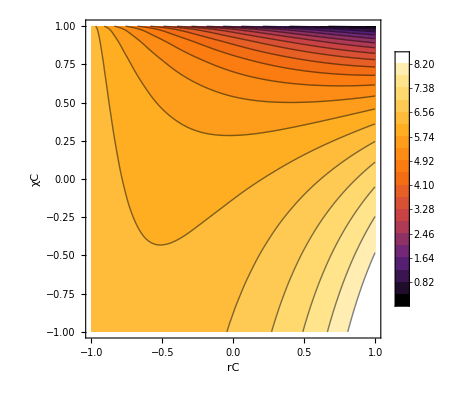

```mathematica
ContourPlot[fInfinityInterp[rC,χC],{rC,-1,1},{χC,-1,1},Contours->20,ContourStyle->Directive[Black,Thin],ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"rC","χC"},AspectRatio->1,PlotPoints->50,PlotRange->All]
```

#### 0 PA energy fluxes

We can finally express the 0PA energy fluxes with respect to the dynamical variables (ν, x, χ):

```mathematica
fluxInf0PA[x_, χ_]:= x^5 /(1-χ x^(3/2))^(10/3) fInfinityInterp[2 KerrGeoISCO[χ, 1]x/(1-χ x^(3/2))^(2/3) -1,χ];
```

```mathematica
fluxHor0PA[x_, χ_]:= x^(15/2) /(1-χ x^(3/2))^(15/3) fHorizonInterp[2 KerrGeoISCO[χ, 1]x/(1-χ x^(3/2))^(2/3) -1,χ];
```

### Energy fluxes in PN

#### Energy flux at null infinity

We have to sum the NS, SO, SS and SSS contributions at 4PN (4.5 PN for NS sector)

```mathematica
fluxInfNS[x_, ν_]:= 32 ν^2 x^5 /5 (1 + (-1247/336 - 35/12 ν)x +4π x^(3/2)+ (-44711/9072 + 9271/504 ν +65/18 ν^2)x^2 +(-8191/672 -583/24 ν)π x^(5/2)+ (6643739519/69854400 + 16/3 π^2 - 1712/105 EulerGamma - 856/105 Log[16x]+(-134543/7776 + 41/48 π^2)ν -94403/3024 ν^2 -775/324 ν^3 )x^3 + (-16285/504 + 214745/1728 ν + 193385/3024 ν^2)π x^(7/2)+(-323105549467/3178375200 + 232597/4410 EulerGamma - 1369/126 π^2 + 39931/294 Log[2]-47385/1568 Log[3]+232597/8820 Log[x]+(-1452202403629/1466942400 + 41478/245 EulerGamma - 267127/4608 π^2 +479062/2205 Log[2] +47385/392 Log[3]+ 20739/245 Log[x])ν +(1607125/6804 -3157/384 π^2)ν^2 + 6875/504 ν^3 +5/6 ν^4 )x^4 + (265978667519/745113600 - 6848/105 EulerGamma - 3424/105 Log[16x]+(2062241/22176 + 41/12 π^2)ν -133112905/290304 ν^2 -3719141/38016 ν^3 )π x^(9/2) );
```

```mathematica
fluxInfSO[x_, ν_,   χ_]:= 32 ν^2 x^(13/2)χ/5(-4 (1+Sqrt[1-4ν])^2 /4 +5/4 Sqrt[1-4ν] (1+Sqrt[1-4ν]) /2 + x((-9/2 +272/9 ν)(1+Sqrt[1-4ν])^2 /4 +(-13/16+43/4 ν)Sqrt[1-4ν] (-(1+Sqrt[1-4ν]) /2) )+x^(3/2)(-16π  (1+Sqrt[1-4ν])^2 /4 +31 π/6  Sqrt[1-4ν](1+Sqrt[1-4ν]) /2) +x^2((476645/6804 +6172/189 ν -2810/27 ν^2)(1+Sqrt[1-4ν])^2 /4 - (9535/336 +1849/126 ν -1501/36 ν^2)Sqrt[1-4ν](1+Sqrt[1-4ν]) /2) +x^(5/2) ((-3485π/96 +13879π/72 ν)(1+Sqrt[1-4ν])^2 /4 - (-7163π/672 +130583π/2016 ν)Sqrt[1-4ν](1+Sqrt[1-4ν]) /2)
);
```

```mathematica
fluxInfSS[x_, ν_, χ_]:= 32 ν^2 x^5 χ^2/5 (x^2(8((1+Sqrt[1-4ν])^2 /4)^2 -8 Sqrt[1-4ν] (1+Sqrt[1-4ν])^2 /4 (1+Sqrt[1-4ν]) /2 +(1/16 -8ν +2)( (1+Sqrt[1-4ν]) /2)^2)+x^3( (-5239/504 -43/2 ν +2(-271/112 -43/4 ν)) ( (1+Sqrt[1-4ν])^2 /4)^2 -(-817/56 +2(-279/56 -43/4 ν) -43/2 ν)Sqrt[1-4ν] (1+Sqrt[1-4ν])^2 /4  (1+Sqrt[1-4ν]) /2 + (-25/8 +344/21 ν +43/2 ν^2 +2 (-279/112 +243/112 ν +43/4 ν^2))(  (1+Sqrt[1-4ν]) /2)^2)+ x^(7/2) (32 π ( (1+Sqrt[1-4ν])^2 /4)^2 -32π Sqrt[1-4ν](1+Sqrt[1-4ν])^2 /4  (1+Sqrt[1-4ν]) /2 +(π/8  -16π ν +2(4π -8π ν))( (1+Sqrt[1-4ν]) /2)^2) + x^4((-4289/648 -295/21 ν +54ν^2 +2(-124577/9072 +3265/126 ν +27ν^2))((1+Sqrt[1-4ν])^2 /4)^2 - (-160621/9072 +9977/252 ν +54ν^2 +2(-74911/4536 +41191/1008 ν +27ν^2))Sqrt[1-4ν](1+Sqrt[1-4ν])^2 /4  (1+Sqrt[1-4ν]) /2 + (1633/336 +465071/18144 ν -74033/1008 ν^2 -54 ν^3 +2(-74911/9072 +102979/2592 ν -7109/168 ν^2 -27ν^3))( (1+Sqrt[1-4ν]) /2)^2)
);
```

```mathematica
fluxInfSSS[x_, ν_, χ_]:= 32 ν^2 x^(17/2)χ^3/5( (-32/3 -8 +40/3)( (1+Sqrt[1-4ν])^2 /4)^3 -(-35/3 -12 +73/3)Sqrt[1-4ν] ( (1+Sqrt[1-4ν])^2 /4)^2  (1+Sqrt[1-4ν]) /2 + (35/6 -12 +32/3 +ν (44/3 +24 -172/3)) (1+Sqrt[1-4ν])^2 /4 ((1+Sqrt[1-4ν]) /2)^2 -(67/12 -4 -1/8 +ν (1 +4 -11))Sqrt[1-4ν]((1+Sqrt[1-4ν]) /2)^3
);
```

Now that we have written every piece, we can write the total PN flux at infinity:

```mathematica
totalPNFluxInf[x_, ν_, χ_]:= fluxInfNS[x, ν] + fluxInfSO[x, ν, χ]+fluxInfSS[x, ν, χ]+fluxInfSSS[x, ν, χ];
```

#### Energy flux at the horizon

We write here the 4PN energy flux at the horizon, using the formula provided by Saketh et al.

```mathematica
B2[χ_]:=Im[PolyGamma[0,3+2 I χ/Sqrt[1-χ^2]]];
```

```mathematica
totalPNFluxHor[x_, ν_, χ_] := -16/5 (1+Sqrt[1-4ν])/2 ν^2 χ x^(15/2) (1+3χ^2 +x/4 (3(2+χ^2)+2(1+Sqrt[1-4ν])/2 (1+3χ^2)(2+3(1+Sqrt[1-4ν])/2)  ) +x^(3/2) (-2(1+Sqrt[1-4ν])/2 (1+3χ^2)((1+Sqrt[1-4ν])/2 χ +4 N[B2[χ], 60]) +(1+Sqrt[1-4ν])/2 (-2/3 (23+30 Sqrt[1-χ^2])χ +(7-12Sqrt[1-χ^2])χ^3)-ν x -3χ^2 ν x +ν χ x^(3/2) +3ν χ^3 x^(3/2))) +16/5 ((1+Sqrt[1-4ν])/2)^2 ν^2 (1+Sqrt[1-χ^2])x^9 (1+3χ^2);
```

### Hybridized fluxes

To get the hybridized expression, we add the 1SF and and 4PN fluxes, and we substract the doubly-counted common terms. This last step amount to factorize the LO behaviour in ν and then set ν to 0. In ‘factorizedPNInfFlux’, we write the PN flux divided by the leading behaviour ν.b2:

```mathematica
factorizedPNInfFlux[x_,ν_,χ_]=Cancel[totalPNFluxInf[x,ν,χ]/ν^2];
```

```mathematica
HybridFluxInf[x_, ν_, χ_]:=ν^2 fluxInf0PA[x, χ]+totalPNFluxInf[x, ν, χ]-ν^2 factorizedPNInfFlux[x, 0, χ];
```

```mathematica
factorizedPNHorFlux[x_,ν_,χ_]=Cancel[totalPNFluxHor[x,ν,χ]/ν^2];
```

```mathematica
HybridFluxHor[x_, ν_, χ_]:=ν^2 fluxHor0PA[x, χ]+totalPNFluxHor[x, ν, χ]-ν^2 factorizedPNHorFlux[x, 0, χ];
```

### Fluxes comparison

#### Fluxes at infinity

Here, we plot the fluxes for 4PN, 0PA and hybrid models. We want an initial mass ratio q=14, which gives an initialsymmetric mass ratio:

```mathematica
nu0=14/15^2;
```

We normalize by the newtonian flux:

```mathematica
fluxNewton[x_,nu_]:=(32/5) nu^2 x^5;
```

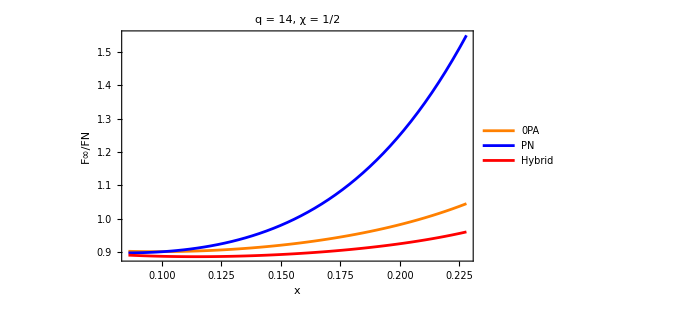
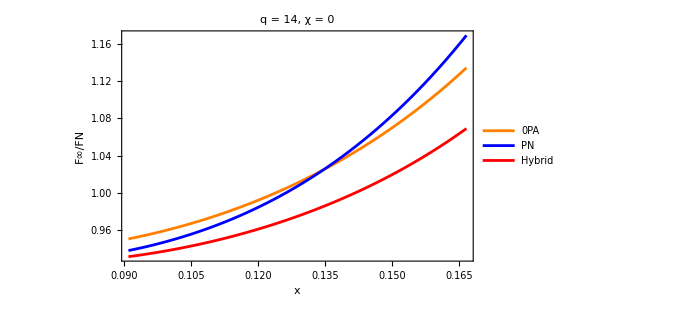
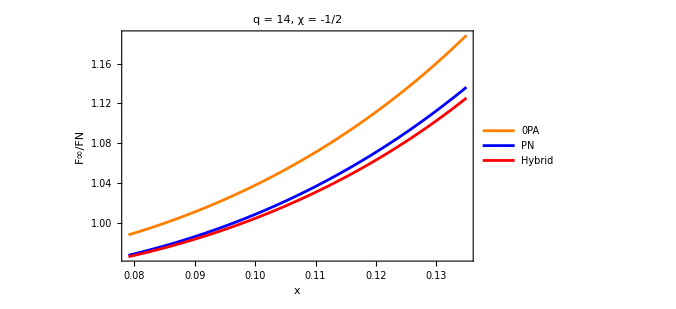

```mathematica
panel[chi0_,xmin_,xmax_]:=Plot[Evaluate[{nu0^2fluxInf0PA[x,chi0],totalPNFluxInf[x,nu0,chi0],HybridFluxInf[x,nu0,chi0]}/fluxNewton[x,nu0]],{x,xmin,xmax},PlotStyle->{Orange,Blue,Red},PlotLegends->{"0PA","PN","Hybrid"},Frame->True,FrameLabel->{"x","F∞/FN"},PlotLabel->Row[{"q = 14, χ = ",chi0}],PlotRange->All,ImageSize->500];

Column[{panel[1/2,0.086,0.228],panel[0,0.091,1/6],panel[-1/2,0.079,0.135]}]
```

#### Total fluxes

```mathematica
total0PAFlux[x_, ν_, χ_]:= ν^2fluxInf0PA[x, χ]+ν^2fluxHor0PA[x, χ];
```

```mathematica
total4PNFlux[x_, ν_, χ_]:= totalPNFluxInf[x, ν, χ]+ totalPNFluxHor[x, ν, χ];
```

```mathematica
totalHybridFlux[x_, ν_, χ_]:= HybridFluxInf[x, ν, χ]+HybridFluxHor[x, ν, χ];
```

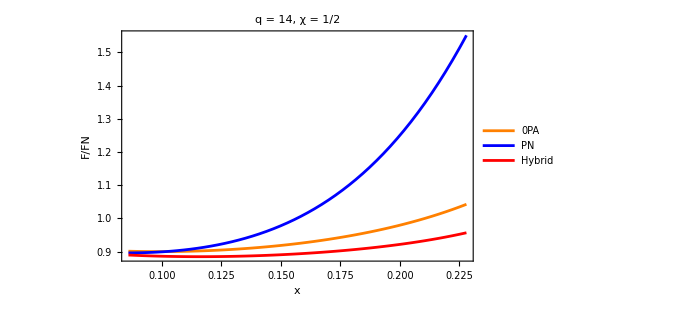
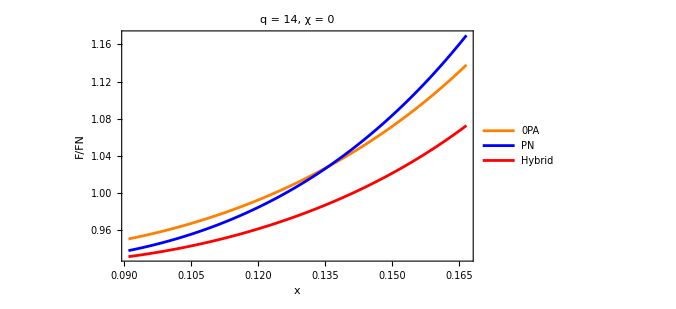
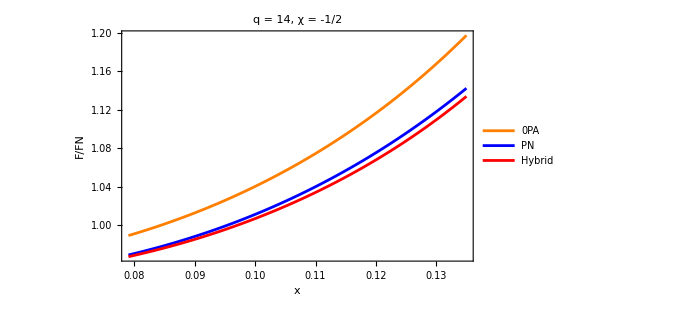

```mathematica
panel[chi0_,xmin_,xmax_]:=Plot[Evaluate[{total0PAFlux[x,nu0, chi0],total4PNFlux[x,nu0,chi0],totalHybridFlux[x,nu0,chi0]}/fluxNewton[x,nu0]],{x,xmin,xmax},PlotStyle->{Orange,Blue,Red},PlotLegends->{"0PA","PN","Hybrid"},Frame->True,FrameLabel->{"x","F/FN"},PlotLabel->Row[{"q = 14, χ = ",chi0}],PlotRange->All,ImageSize->500];

Column[{panel[1/2,0.086,0.228],panel[0,0.091,1/6],panel[-1/2,0.079,0.135]}]
```

## Computation of the binding energy

### Binding energy in SF

#### 0PA binding energy

At leading SF order, it is the geodesic binding energy, that we can express directly as a function of χ:

```mathematica
geoBindingEnergy[x_, χ_]:= -1 +(1-2x (1-x^(3/2) χ )^(1/3))/Sqrt[(1-x^(3/2) χ )(1+x^(3/2)χ -3x(1-x^(3/2) χ )^(1/3))];
```

We now want to compute the leading order correction to the binding energy. This correction is linked to the first order correction to the Detweiler redshift invariant.

#### Interpolation of the first order correction of z

I haven’t found yet how to recover the data needed for the interpolation...

### Binding energy in PN

For the non-spinning term, one has to take into account the Schott term that arises at 4PN. This was shown to be equivalent to taking the 4PN mechanical energy and replacing yPN by x (see Trestini 2025).

Moreover, we express here the adimensionned binding energies (divided by M).

```mathematica
bindingEnergyNS[x_, ν_]:=-ν x /2 (1-(3/4 + ν/12)x +(-27/8+19/8 ν -ν^2 /24)x^2 +(-675/64 +(34445/576 -205 π^2/96)ν -155/96 ν^2 -35/5184 ν^3)x^3 +(-3969/128 +(9037 π^2/1536 -123671/5760 +448/15 (2EulerGamma +Log[16 x]))ν +(3157/576 π^2 -498449/3456)ν^2 +301/1728 ν^3 +77/31104 ν^4)x^4);
```

In the spin sectors, the Schott term correction is above 4PN, we can then use yPN and x interchangeably.

```mathematica
bindingEnergySO[x_, ν_, χ_]:= -ν χ/2 x^(5/2) (14/3 (1+Sqrt[1-4ν])^2 /4 -(1+Sqrt[1-4ν])Sqrt[1-4ν] +x((11-61/9 ν)(1+Sqrt[1-4ν])^2 /4 -(3-10/3 ν)(1+Sqrt[1-4ν])Sqrt[1-4ν]/2)+x^2 ((135/4 -367/4 ν +29/12 ν^2)(1+Sqrt[1-4ν])^2 /4 -(27/4 -39ν+5/4ν^2)(1+Sqrt[1-4ν])Sqrt[1-4ν]/2));
```

```mathematica
bindingEnergySS[x_, ν_, χ_]:= -ν χ^2 /2 x^3 (-4((1+Sqrt[1-4ν])^2 /4)^2 +4(1+Sqrt[1-4ν])^2 /4 (1+Sqrt[1-4ν])/2 Sqrt[1-4ν] +((1+Sqrt[1-4ν])/2)^2 (-1+4ν)+x (((1+Sqrt[1-4ν])^2 /4)^2 (-25/3 +50/9+10/3 ν) -(1+Sqrt[1-4ν])^2 /4 (1+Sqrt[1-4ν])/2 Sqrt[1-4ν] (-5+25/3+10/3 ν)+((1+Sqrt[1-4ν])/2)^2 (-5/2 +5+ν(5/2-10)+10/3 ν^2))+x^2 ((67/12 +6445/108 ν-7/36 ν^2 +2 (-125/8 +1025/72 ν -7/72 ν^2))((1+Sqrt[1-4ν])^2 /4)^2 -(49/4 +1649/36 ν -7/36 ν^2 +2 (-63/8 +295/24 ν -7/72 ν^2))Sqrt[1-4ν](1+Sqrt[1-4ν])^2 /4 (1+Sqrt[1-4ν])/2 +(21/2 -119/12 ν -135/4 ν^2 +7/36 ν^3 +2(-63/16 +301/48 ν -499/48 ν^2 +7/72ν^3))((1+Sqrt[1-4ν])/2)^2));
```

```mathematica
bindingEnergySSS[x_, ν_, χ_]:= -ν χ^3 /2 x^(9/2)(-8 ((1+Sqrt[1-4ν])^2 /4)^3 +16 ((1+Sqrt[1-4ν])^2 /4)^2 Sqrt[1-4ν] (1+Sqrt[1-4ν])/2 +(-10+40 ν)(1+Sqrt[1-4ν])^2 /4 ((1+Sqrt[1-4ν])/2)^2 -(-2+8ν)Sqrt[1-4ν]((1+Sqrt[1-4ν])/2)^3);
```

Now that we have written every piece, we can write the total 4PN binding energy:

```mathematica
totalBindingEnergy4PN[x_, ν_, χ_]:= bindingEnergyNS[x, ν]+bindingEnergySO[x, ν, χ]+bindingEnergySS[x, ν, χ]+bindingEnergySSS[x, ν, χ];
```

### Hybrid binding energy

To get the hybridized expression, we add the 1SF and and 4PN binding energies, and we substract the doubly-counted common terms. This last step amount to factorize the LO behaviour in ν and then set ν to 0. In ‘factorizedBindingEnergy4PN’, we write the PN binding energy divided by the leading behaviour ν:

```mathematica
factorizedBindingEnergy4PN[x_,ν_,χ_]=Cancel[totalBindingEnergy4PN[x,ν,χ]/ν];
```

```mathematica
HybridBindingEnergy[x_, ν_, χ_]:=ν geoBindingEnergy[x, χ]+totalBindingEnergy4PN[x, ν, χ]-ν factorizedBindingEnergy4PN[x,0,χ];
```

### Comparison of the binding energy for the different models

To compare the binding energies from the different models, we shift them so they all vanish at t_initial.

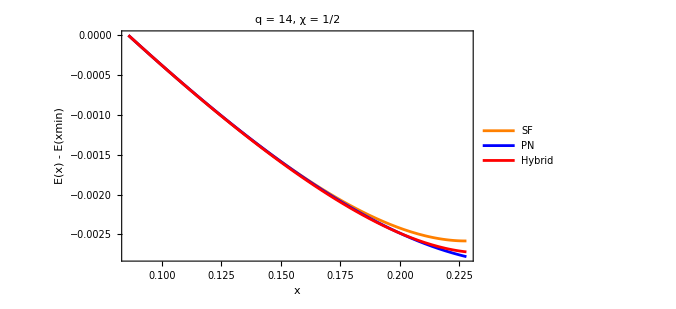
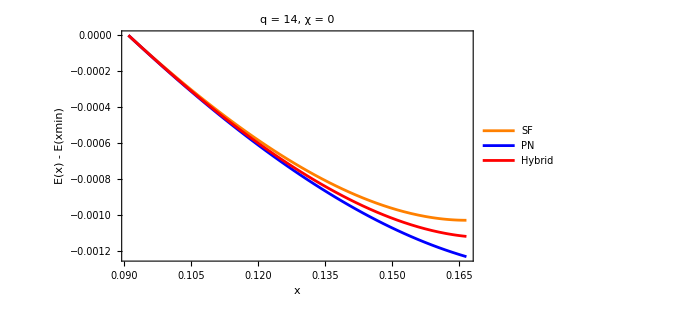
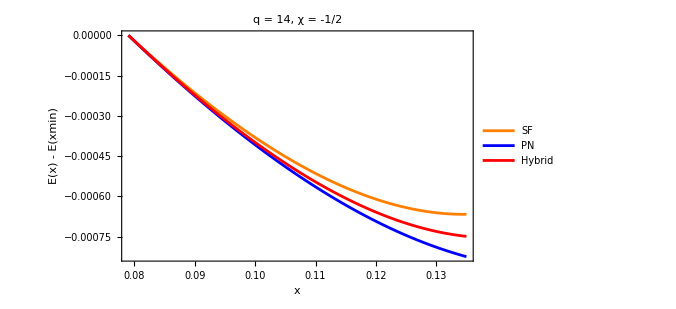

```mathematica
nu0=14/15^2;

panelEnergy[χ0_,xmin_,xmax_]:=Plot[Evaluate[{nu0 geoBindingEnergy[x,χ0 ]-nu0 geoBindingEnergy[xmin,χ0 ],totalBindingEnergy4PN[x,nu0,χ0]-totalBindingEnergy4PN[xmin,nu0,χ0],HybridBindingEnergy[x,nu0,χ0]-HybridBindingEnergy[xmin,nu0,χ0]}],{x,xmin,xmax},PlotStyle->{Orange,Blue,Red},PlotLegends->{"SF","PN","Hybrid"},Frame->True,FrameLabel->{"x","E(x) - E(xmin)"},PlotLabel->Row[{"q = 14, χ = ",χ0}],PlotRange->All,ImageSize->500];

Column[{panelEnergy[1/2,0.086,0.228],panelEnergy[0,0.091,1/6],panelEnergy[-1/2,0.079,0.135]}]
```

## Computation of mode amplitudes

### Mode amplitudes in SF

#### Evaluate the spherical harmonics coeff at the nodes

In SF, the amplitudes are expressed in the spheroidal harmonics basis, while in PN the spherical harmonics basis is used. To hybridize the expression, one may first express the SF amplitudes in the spherical harmonics basis, ie perform a change of basis. The Teukolsky package gives the coeff needed. First, we construct the Chebyshev grid (same as before):

```mathematica
nR = 18;
nχ = 27;

nodesX = Table[Cos[(2 i +1)π /(2 nR )], {i, 0, nR-1}];
nodesY = Table[Cos[(2 j +1)π /(2 nχ )], {j, 0, nχ-1}];
lmax = 5;
Ndigit = 64;
```

Then, the function giving the spherical coeff for a point in the grid:

Finally, we evaluate the function on the 2D grid:

We stock the data on a file, to avoid computing it every time:

#### Chebyshev interpolation

### Mode amplitudes in PN

Here, we write the PN amplitudes for a (2 2) mode amplitude chosen to be real-valued. 4PN expression of the (2 2) mode:

```mathematica
ampl22[x_, ν_]:= Sqrt[64 π/5]ν x (1+ (-107/42 +55/42 ν)x +2 π x^(3/2) +(-2173/1512 - 1069/216 ν +2047/1512 ν^2)x^2 + (-107/21 +34/21 ν)π x^(5/2)+ (27027409/646800 -856/105 EulerGamma +2π^2/3 +(-278185/33264 +41π^2/96)ν -20261/2772 ν^2 +114635/99792 ν^3 -428/105 Log[16 x])x^3 +(-2173/756 -2495/378 ν +40/27 ν^2)π x^(7/2)+(-846557506853/12713500800 +45796/2205 EulerGamma -107/63 π^2 +22898/2205 Log[16 x] +(-336005827477/4237833600 +15284/441 EulerGamma -9755/32256 π^2 +7642/441 Log[16 x])ν +(256450291/7413120 -1025/1008 π^2)ν^2 -81579187/15567552 ν^3 +26251249/31135104 ν^4)x^4) ;
```